```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]];
macSize = 500;linSize = 1000;
SetOptions[{MatrixPlot,ListVectorPlot},ImageSize->linSize,ImagePadding->{{50,70},{50,50}},LabelStyle->{Directive["Times",14,Black],FontFamily->"Times"}];
SetOptions[{ListPlot,ListLogPlot,ListLogLogPlot,Plot,LogPlot,LogLogPlot,Histogram},Frame->True,AspectRatio->1/GoldenRatio,ImageSize->linSize,LabelStyle->{Directive["Times",18,Black],FontFamily->"Times",ImagePadding->{{100,100},{100,100}}}];
```

## Functions

```mathematica
getData[type_,T_,H_,A_,ED_,PMA_]:=Block[{relDir,fileSuffix,data},

relDir="data/thermal-collapse-data/";
fileSuffix ="_T="<>ToString[T]<>"_H="<>ToString[H]<>"_DMI="<>ToString[A]<>"_DDI="<>ToString[ED]<>"_PMA="<>ToString[PMA]<>"_*.h5";

Which[
type=="relaxation-spin",
data=ToExpression[Import["data/thermal-collapse-data/spin_field_after_relaxation"<>fileSuffix,"Data"]],

type=="relaxation-energy",
data=ToExpression[Import["data/thermal-collapse-data/energy_during_relaxation"<>fileSuffix,"Data"]],

type=="relaxation-topcharge",
data=ToExpression[Import["data/thermal-collapse-data/topological_charge_during_relaxation"<>fileSuffix,"Data"]],

type=="relaxation-size",
data=ToExpression[Import["data/thermal-collapse-data/effective_size_during_relaxation"<>fileSuffix,"Data"]]

];
data[[1,1]]
]
```

# Plot relaxation results

```mathematica
Tchoice="0.0";
Hchoice=-0.0014;
Achoice=0.02EDchoice="0.0";
PMAchoice="0.0";
```

Spin field

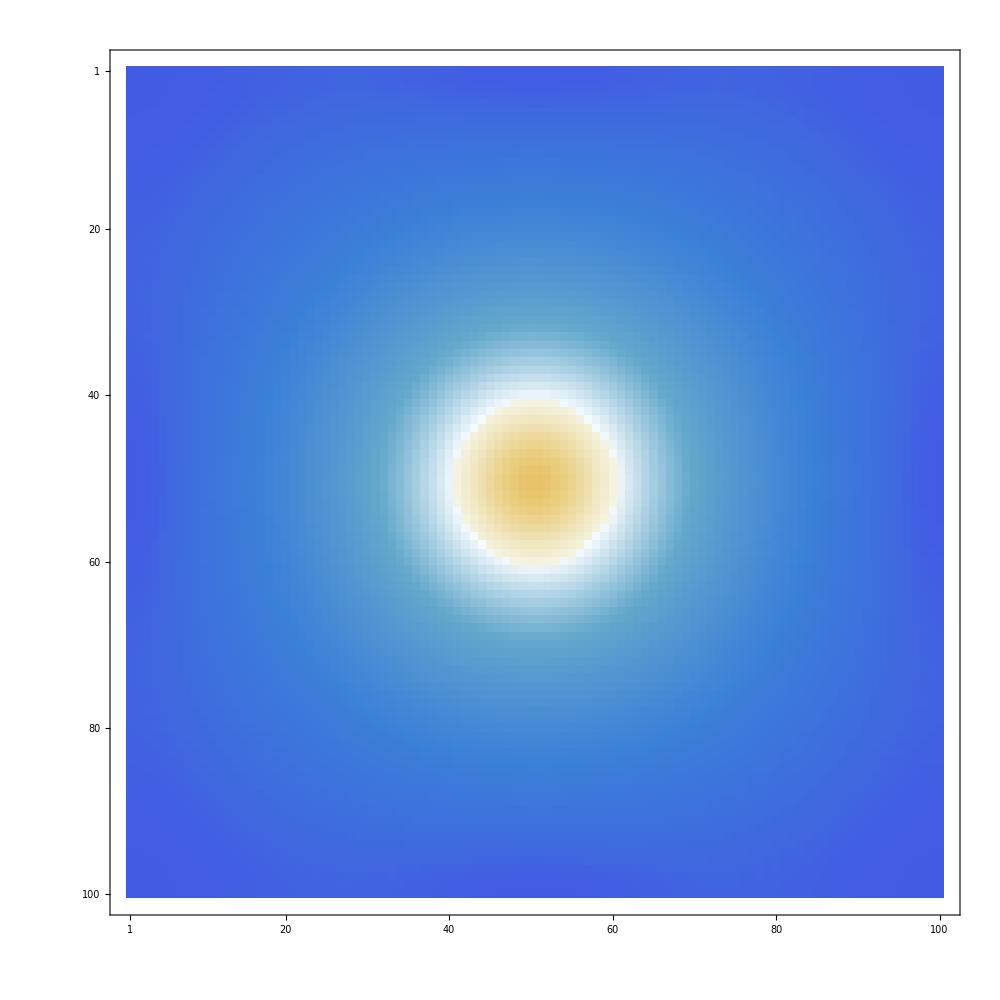

```mathematica
spindata=getData["relaxation-spin",Tchoice,Hchoice,Achoice,EDchoice,PMAchoice];
MatrixPlot[spindata[[All,All,3]]]
```

Plot energy during relaxation

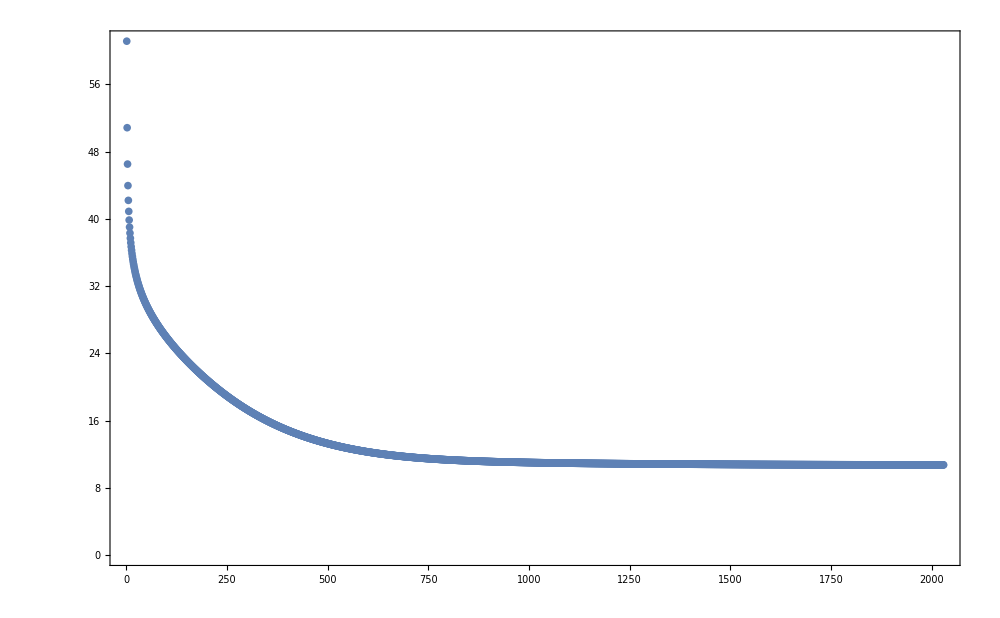

```mathematica
endata=getData["relaxation-energy",Tchoice,Hchoice,Achoice,EDchoice,PMAchoice];
ListPlot[endata,PlotRange->All]
```

Plot effective size during relaxation

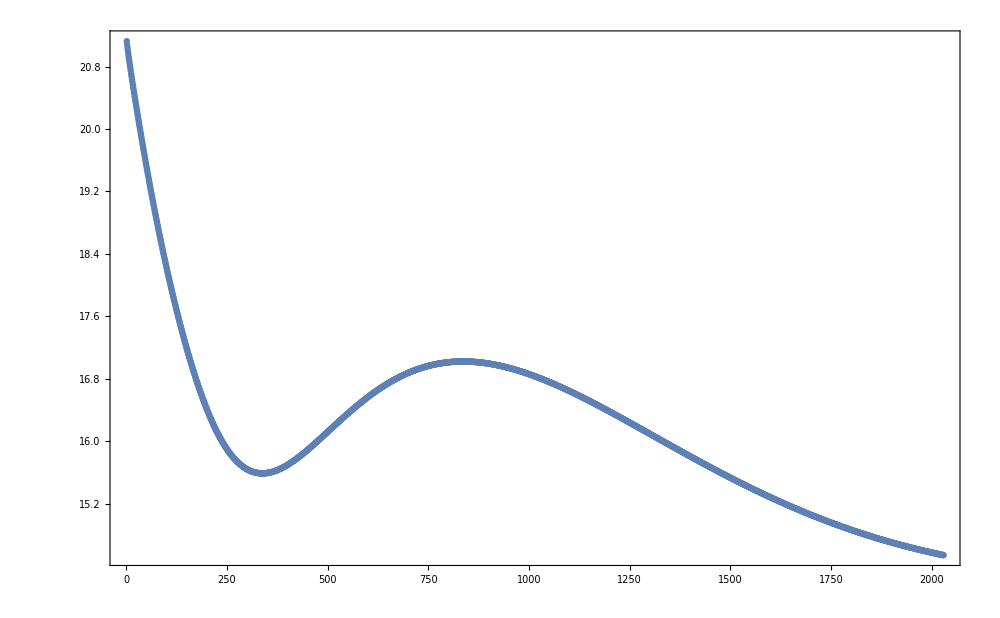

```mathematica
esdata=getData["relaxation-size",Tchoice,Hchoice,Achoice,EDchoice,PMAchoice];
ListPlot[esdata,PlotRange->All]
```

Plot topological charge during relaxation

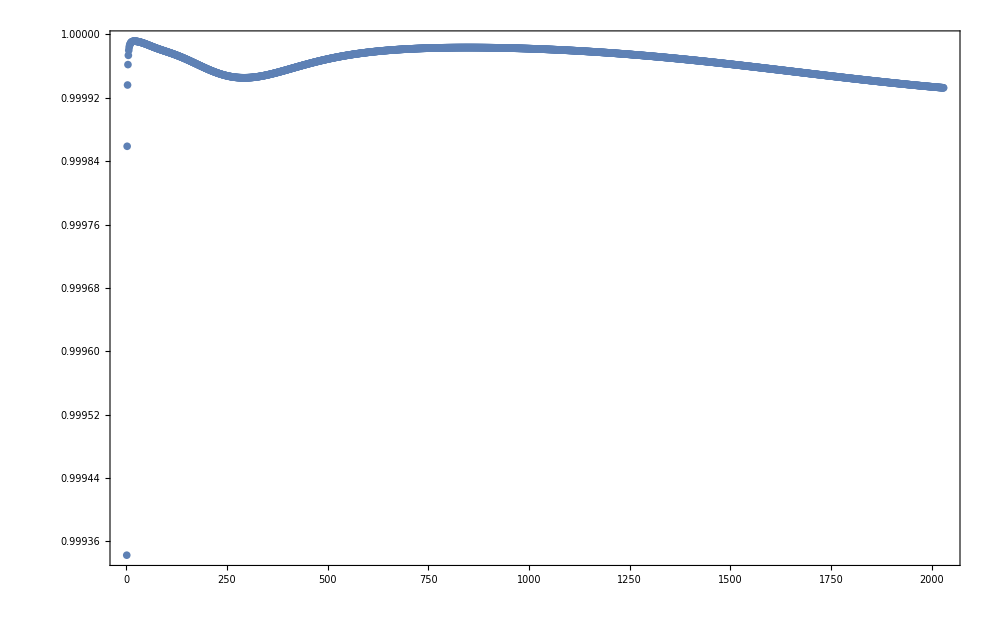

```mathematica
tcdata=getData["relaxation-topcharge",Tchoice,Hchoice,Achoice,EDchoice,PMAchoice];
ListPlot[tcdata,PlotRange->All]
```